```mathematica
f[k_] := 1/k;
suma =Sum[(-1)^(k-1)*f[k], {k, 1, Infinity}] (*1*)
```

Log[2]

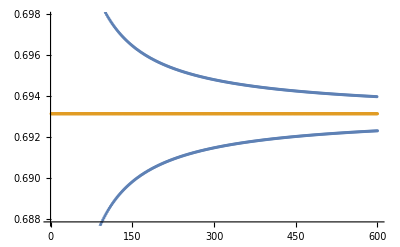

```mathematica
n = 600; (*2*)
series = Table[(-1)^(k-1)*f[k],{k,1,n}] ;
partial=Accumulate[series];
ListPlot[{partial,Table[Log[2],{i,1,n}]}]
```

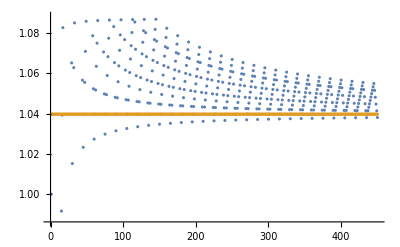

```mathematica
(*3*)
p = 10;
q = 5;
rep = 30;
ser = Table[(-1)^(k-1)*f[k], {k, 1, n}];
pos = Partition[Select[ser, (# > 0)&,  rep*p], p] ;
neg = Partition[Select[ser, (# < 0)&,  rep*q], q] ;
s =Flatten[ Table[{pos[[k]],neg[[k]]}, {k, 1, rep}]];
K =  Limit[k*f[k],k->Infinity];
Ocekavani = suma + 1/2 * K * Log[p/q];

ListPlot[{Accumulate[s], Table[Ocekavani, {x, 1, rep*(p+q)}]}]
```

```mathematica
(*4*)
g[x_]:=f[x];
cislo = 1.3;
prerovnani:=(
suma = Sum[(-1)^(k-1)*g[k], {k, 1, Infinity}] ;
K = Limit[k*g[k],k->Infinity];
pomer = N[Exp[2*(cislo - suma)/K ]];
pomer = Rationalize[pomer,10^(-2)];
p = Numerator[pomer];
q = Denominator[pomer];

rep = 10;
ser = Table[(-1)^(k-1)*f[k], {k, 1,2*rep* (p+q + 2)}];
pos = Partition[Select[ser, (# > 0)&,  rep*p], p] ;
neg = Partition[Select[ser, (# < 0)&,  rep*q], q] ;
s =Flatten[ Table[{pos[[k]],neg[[k]]}, {k, 1, rep}]];
ListPlot[{Accumulate[s], Table[cislo, {x, 1, rep*(p+q)}]}]
)
f
prerovnani[(f[#])&,1.3]
```

f

NSum::nsnum: Summand (or its derivative) (-1)^(-1+k) f[k] is not numerical at point k = 46662.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

Table::iterb: Iterator {k,1,20 (3+(19/7)^((2 (13/10-NSum[«2»]))/Limit[Times[«2»],Rule[«2»]]))} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Select::innf: Non-negative integer or Infinity expected at position 3 in Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^(2 Power[«2»] Plus[«2»]))}],#1>0&,10 (19/7)^((2 (13/10-NSum[Times[«2»],{«3»}]))/(lim_(k→DirectedInfinity[«1»]) k f[«1»]))].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^Times[«3»])}],#1>0&,10 (19/7)^((2 (13/10-NSum[«2»]))/Limit[Times[«2»],Rule[«2»]])],(19/7)^((2 (13/10-NSum[Power[«2»] f[«1»],{k,1,DirectedInfinity[«1»]}]))/(lim_(k→∞) k f[k]))].

Select::innf: Non-negative integer or Infinity expected at position 3 in Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^(2 Power[«2»] Plus[«2»]))}],#1>0&,10 (19/7)^((2 (13/10-NSum[Times[«2»],{«3»}]))/(lim_(k→DirectedInfinity[«1»]) k f[«1»]))].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^Times[«3»])}],#1>0&,10 (19/7)^((2 (13/10-NSum[«2»]))/Limit[Times[«2»],Rule[«2»]])],(19/7)^((2 (13/10-NSum[Power[«2»] f[«1»],{k,1,DirectedInfinity[«1»]}]))/(lim_(k→∞) k f[k]))].

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Limit::ivar: 1 is not a valid variable.

Select::innf: Non-negative integer or Infinity expected at position 3 in Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^(2 Power[«2»] Plus[«2»]))}],#1>0&,10 (19/7)^((2 (13/10-NSum[Times[«2»],{«3»}]))/(lim_(1→DirectedInfinity[«1»]) f[1]))].

General::stop: Further output of Select::innf will be suppressed during this calculation.

Limit::ivar: 1 is not a valid variable.

General::stop: Further output of Limit::ivar will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^Times[«3»])}],#1>0&,10 (19/7)^((2 (13/10-NSum[«2»]))/Limit[f[«1»],Rule[«2»]])],(19/7)^((2 (13/10-NSum[Power[«2»] f[«1»],{k,1,DirectedInfinity[«1»]}]))/(lim_(1→∞) f[1]))].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Part::partw: Part 1 of Table[] does not exist.

Part::partw: Part 2 of Table[] does not exist.

Part::partw: Part 3 of Partition[Select[Table[(-1)^(k-1) f[k],{k,1,20 (3+(19/7)^Times[«3»])}],#1>0&,10 (19/7)^((2 (13/10-NSum[«2»]))/Limit[Times[«2»],Rule[«2»]])],(19/7)^((2 (13/10-NSum[Power[«2»] f[«1»],{k,1,DirectedInfinity[«1»]}]))/(lim_(3→∞) 3 f[3]))] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.